```mathematica
k=1.0
```

1.

```mathematica
a=0.05
```

0.05

```mathematica
xfunc[t_,x_,v_]=v
```

v

```mathematica
vfunc[t_,x_,v_]=-k x - a x^3
```

-1. x-0.05 x^3

```mathematica
RK4[ti_, xi_, vi_, h_, tf_]:=(
Lx={{ti, xi}};
Lv={{ti,vi}};
x = xi;
v = vi;
For[t=ti+h,t≤tf,t+=h,
k1=h*xfunc[t+h/2,x, v];
m1 = h*vfunc[t+h/2, x, v];

k2=h*xfunc[t+h/2, x+k1/2, v+m1/2];
m2=h*vfunc[t+h/2, x+k1/2, v+m1/2];

k3=h*xfunc[t+h/2, x+k2/2, v+m2/2];
m3=h*vfunc[t+h/2, x+k2/2, v+m2/2];

k4=h*xfunc[t+h,x+k3, v+m3];
m4=h*vfunc[t+h, x+k3, v+m3];

x+=(k1 + 2 k2 + 2 k3 + k4)/6;
v+= (m1 + 2 m2 + 2 m3 + m4)/6;

Lx = Append[Lx, {t,x}];
Lv = Append[Lv, {t,v}];
];

Return[{Lx,Lv}];
)
```

```mathematica
sols = RK4[0,1, 0, 0.1, 10];
```

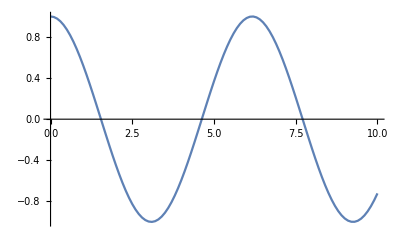

```mathematica
ListLinePlot[sols[[1]]]
```

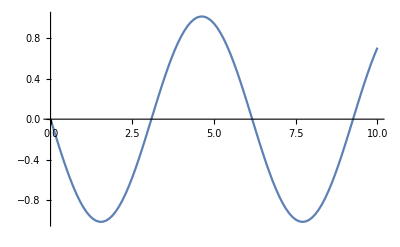

```mathematica
ListLinePlot[sols[[2]]]
```